```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
colors={Black,Red,Blue,Green};
```

```mathematica
lvecsfcc={{1,0},{Cos[π/3],Sin[π/3]}};
```

#### Hopping rates

```mathematica
khop[D_,l_] := D 4/l^2
```

```mathematica
khop[10^-6.3, 2.77 10^-8]
```

2.61277×10^9

## MMC

```mathematica
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc\\O-Pt"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt

```mathematica
{TogglerBar[Dynamic[cfiles],FileNames["*.confs"],Appearance->"Vertical"],TogglerBar[Dynamic[efiles],FileNames["*.en"],Appearance->"Vertical"],TogglerBar[Dynamic[hfiles],FileNames["*.hist"],Appearance->"Vertical"]}
```

{









,









,


}

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nrows,ncols,Tstep}=data[[All,2]]ᵀ;
snames=data[[All,3]];
pos=Position [Flatten[#,0],"step"][[All,1]]&/@data;
steps=Table[data[[ifiles,pos[[ifiles,step]],3]],{ifiles,Length[data]},{step,Length[pos[[ifiles]]]}];
nads=Table[data[[ifile,pos[[ifile,i]]+1]],{ifile,Length[data]},{i,Length[pos[[ifile]]]}];
adslist=Table[data[[ifile,pos[[ifile,i]]+2;;pos[[ifile,i]]+2+Total[nads[[ifile,i]]]-1]],{ifile,Length[data]},{i,Length[pos[[ifile]]]}];
occs=Table[Normal[SparseArray[adslist[[ifile,i,All,{2,3}]]->adslist[[ifile,i,All,1]],{nrows[[ifile]],ncols[[ifile]]}]],{ifile,Length[adslist]},{i,Length[pos[[ifile]]]}];
data = .
```

```mathematica
energy=Import[#,"Table"]&/@efiles;
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
hrefs=Position[#,"counts"][[All,1]]&/@data;
ncounts=Table[data[[ifile,hrefs[[ifile]],2]],{ifile,Length[data]}];
nspecies=Table[(Differences[Append[hrefs[[ifile]],Length[data[[ifile]]]+1]]-1)/2,{ifile,Length[data]}];
hist=Table[data[[ifile,hrefs[[ifile,i]]+2species]],{ifile,Length[data]},{i,Length[hrefs[[ifile]]]},{species,nspecies[[ifile,i]]}];
(* hist[ file, record, species, number of clusters ] *)
data=.
```

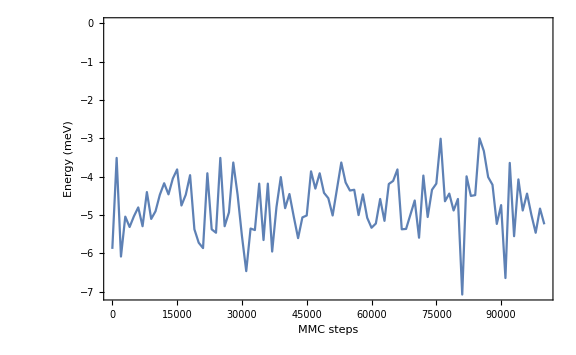

```mathematica
ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

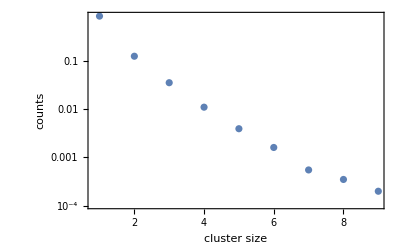

```mathematica
ListLogPlot[Flatten[Table[hist[[i,-1]]/(Total/@(hist[[i,-1]])),{i,Length[hfiles]}],1],FrameLabel->{"cluster size","counts"},PlotRange->{All,All}]
```

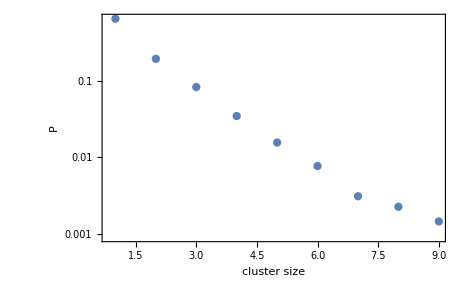

```mathematica
csize=Table[Range[1,Length/@(hist[[i,-1]])],{i,Length[hfiles]}];
pnew=ListLogPlot[Flatten[Table[(csize[[i]]hist[[i,-1]])/(ncounts[[i,-1]]nads[[i,-1]]),{i,Length[hfiles]}],1],FrameLabel->{"cluster size","P"},PlotRange->{All,All}]
```

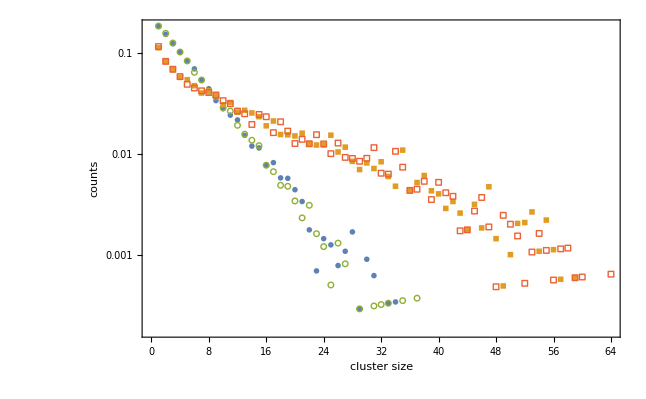

```mathematica
adslists=Map[Gather[#,#1[[5]]==#2[[5]]&]&,adslist,{2}];
latframes=Table[Graphics[{Text["step = "<>ToString[steps[[ifiles,step]]],Scaled[{.05,.95}]],Table[{colors[[i]],Disk[#,.4]&/@({adslists[[ifiles,step,i,All,3]],nrows[[ifiles]]-adslists[[ifiles,step,i,All,2]]}ᵀ.lvecsfcc)},{i,Length[adslists[[ifiles,step]]]}]},PlotRange->{{-1,-1},{ncols[[ifiles]],nrows[[ifiles]]}.lvecsfcc}ᵀ,ImageSize->600],{ifiles,Length[adslists]},{step,Length[adslists[[ifiles]]]}];
Manipulate[latframes[[system,frame]],{system,Thread[Range[1,Length[pos]]->(FileBaseName/@cfiles)]},{frame,1,Length[pos[[system]]],1}]
```

Part::partd: Part specification latframes⟦2,92⟧ is longer than depth of object.

## KMC

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\bkl\\O-Pt"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\bkl\O-Pt

```mathematica
cfiles=FileNames["*.confs"]
efiles=FileNames["*.en"]
hfiles=FileNames["*.hist"]
mmcefiles=FileNames["*.en","C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc\\O-Pt"]
mmchfiles=FileNames["*.hist","C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc\\O-Pt"]
```

{0020x0020-O_02500-T0600000001.confs,0020x0020-O_02500-T1000000001.confs}

{0020x0020-O_02500-T0600000001.en,0020x0020-O_02500-T1000000001.en}

{0020x0020-O_02500-T0600000001.hist,0020x0020-O_02500-T1000000001.hist}

{C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T0600.en,C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T0600-eq.en,C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T1000.en,C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T1000-eq.en,C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T1000-melt.en}

{C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T0600.hist,C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-Pt\0020x0020-O_02500-T1000.hist}

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nrows,ncols,Tstep}=data[[All,2]]ᵀ;
snames=data[[All,3]];
pos=Position [Flatten[#,0],"time"][[All,1]]&/@data;
time=Table[data[[ifiles,pos[[ifiles,step]],2]],{ifiles,Length[data]},{step,Length[pos[[ifiles]]]}];
nads=Table[data[[ifile,pos[[ifile,i]]+1]],{ifile,Length[data]},{i,Length[pos[[ifile]]]}];
adslist=Table[data[[ifile,pos[[ifile,i]]+2;;pos[[ifile,i]]+2+Total[nads[[ifile,i]]]-1]],{ifile,Length[data]},{i,Length[pos[[ifile]]]}];
occs=Table[Normal[SparseArray[adslist[[ifile,i,All,{2,3}]]->adslist[[ifile,i,All,1]],{nrows[[ifile]],ncols[[ifile]]}]],{ifile,Length[adslist]},{i,Length[pos[[ifile]]]}];
data = .
```

```mathematica
energy=Import[#,"Table"]&/@efiles;
```

```mathematica
mmcenergy=Import[#,"Table"]&/@mmcefiles;
```

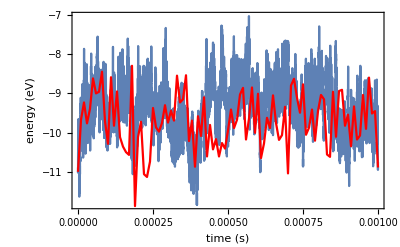

```mathematica
pbklen=ListLinePlot[{energy[[1,All,1]],energy[[1,All,2]]}ᵀ,FrameLabel->{"time (s)","energy (eV)"}];
pmmcen=ListLinePlot[{mmcenergy[[1,All,1]] 10^-8,mmcenergy[[1,All,2]]}ᵀ,FrameLabel->{"step","energy (eV)"},PlotStyle->Red];
Show[pbklen,pmmcen]
```

```mathematica
data=Import[#,"Table"]&/@mmchfiles;
hrefs=Position[#,"counts"][[All,1]]&/@data;
ncounts=Table[data[[ifile,hrefs[[ifile]],2]],{ifile,Length[data]}];
nspecies=Table[(Differences[Append[hrefs[[ifile]],Length[data[[ifile]]]+1]]-1)/2,{ifile,Length[data]}];
mmchist=Table[data[[ifile,hrefs[[ifile,i]]+2species]],{ifile,Length[data]},{i,Length[hrefs[[ifile]]]},{species,nspecies[[ifile,i]]}];
(* hist[ file, record, species, number of clusters ] *)
data=.
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
hrefs=Position[#,"time"][[All,1]]&/@data;
time=Table[data[[ifile,hrefs[[ifile]],2]],{ifile,Length[data]}];
nspecies=Table[(Differences[Append[hrefs[[ifile]],Length[data[[ifile]]]+1]]-1)/2,{ifile,Length[data]}];
hist=Table[data[[ifile,hrefs[[ifile,i]]+2species]],{ifile,Length[data]},{i,Length[hrefs[[ifile]]]},{species,nspecies[[ifile,i]]}];
(* hist[ file, record, species, number of clusters ] *)
data=.
```

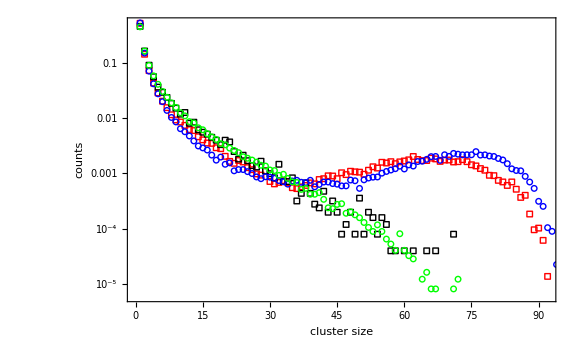

```mathematica
pmmch=ListLogPlot[Flatten[Table[Mean[mmchist[[i]]]/(Total/@Mean[mmchist[[i]]]),{i,Length[mmchfiles]}],1],FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{Style["○", Small, Blue],Style["○", Small, Green]}];
pbklh=ListLogPlot[Flatten[Table[Mean[hist[[i]]]/(Total/@Mean[hist[[i]]]),{i,Length[hfiles]}],1],FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{Style["□", Medium, Red],Style["□", Medium, Black]}];
Show[pbklh,pmmch]
```

## Compare MMC and KMC

### nlat020T1000c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc\\nlat020T1000c0250"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc\nlat020T1000c0250

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en,mmc_eq_i005.en,mmc_i005.en,mmc_melt.en,mmc_melt_i005.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

{{20,20,20,20,20,20},{100,100,100,100,100,100}}

{1001,101,101,1001,101,101}

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[All,2;;;;2]]];
kmchist=data[[All,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[-1,All,2]]],Variance[energy[[-1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-8.52703,3.54062}

{-0.92454,0.0483257}

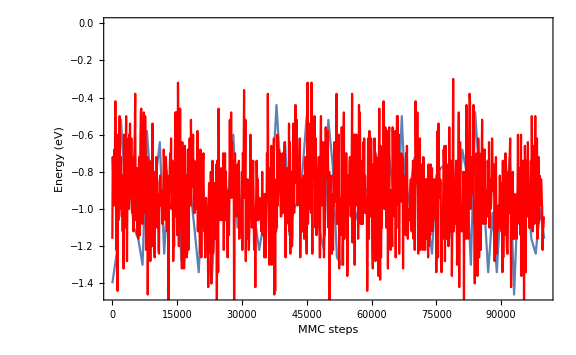

```mathematica
Show[ListLinePlot[energy[[2]],PlotRange->All,FrameLabel->{"MMC steps","Energy (eV)"},ImageSize->Large],kmcenplot]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1,1 1.5nlat[[1]]},{-1,1nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

Part::partd: Part specification nlat⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-1,1.5 nlat⟦1⟧},{-1,nlat⟦1⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partd: Part specification nlat⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-1,1.5 nlat⟦1⟧},{-1,nlat⟦1⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
itr=-1;
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[itr,i]],nlat[[itr]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[itr]]},{-3,3nlat[[itr]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[itr]],1}]
```

Part::pkspec1: The expression itr cannot be used as a part specification.

ArrayPad::arr: First argument «1» to ArrayPad should be an array.

Part::pkspec1: The expression itr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {1,1,1,1,2}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,7}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,19}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 2}, {-1, -1} + {1, <<3>>, 7}, <<255023>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 nlat⟦itr⟧},{-3,3 nlat⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1., -1.} + {1., 1., 1., 1., 2.}, <<255024>>, {3.} + {-1., -1.}} . {<<2>>} is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 nlat⟦itr⟧},{-3,3 nlat⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1., -1.} + {1., 1., 1., 1., 2.}, <<255024>>, {3.} + {-1., -1.}} . {<<2>>} is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression itr cannot be used as a part specification.

ArrayPad::arr: First argument «1» to ArrayPad should be an array.

Part::pkspec1: The expression itr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {1,1,1,1,1}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,9}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,10}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<265225>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 nlat⟦itr⟧},{-3,3 nlat⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1., -1.} + {1., 1., 1., 1., 1.}, <<265226>>} . {{1., 0.}, {<<2>>}} is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 nlat⟦itr⟧},{-3,3 nlat⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1., -1.} + {1., 1., 1., 1., 1.}, <<265226>>} . {{1., 0.}, {<<2>>}} is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression itr cannot be used as a part specification.

ArrayPad::arr: First argument {{{{82, 0, 0, <<15>>, 78, 20}, <<19>>}, <<1000>>}, <<5>>}[[itr,66]] to ArrayPad should be an array.

Thread::tdlen: Objects of unequal length in {1,1,1,1,1}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,4}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,13}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<240599>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

Part::pkspec1: The expression itr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<240599>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 {20,20,20,20,20,20}⟦itr⟧},{-3,3 {20,20,20,20,20,20}⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1., -1.} + {1., 1., 1., 1., 1.}, <<240600>>} . {{1., 0.}, {<<2>>}} is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression itr cannot be used as a part specification.

ArrayPad::arr: First argument {{{{82, 0, 0, <<15>>, 78, 20}, <<19>>}, <<1000>>}, <<5>>}[[itr,66]] to ArrayPad should be an array.

Thread::tdlen: Objects of unequal length in {1,1,1,1,1}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,4}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,13}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<240599>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

Part::pkspec1: The expression itr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<240599>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 {20,20,20,20,20,20}⟦itr⟧},{-3,3 {20,20,20,20,20,20}⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1., -1.} + {1., 1., 1., 1., 1.}, <<240600>>} . {{1., 0.}, {<<2>>}} is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression itr cannot be used as a part specification.

ArrayPad::arr: First argument {{{{56,100,89,0,0,0,0,0,0,57,0,0,18,0,0,0,0,0,0,72},{24,0,69,48,0,0,0,0,0,0,0,0,17,0,0,54,0,71,27,73},{8,0,0,101,98,0,0,0,0,59,0,0,22,0,0,0,0,0,65,91},«14»,{77,0,28,45,0,0,5,19,50,0,40,0,0,0,76,0,0,0,0,0},{3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,83,0,0,0,0},{62,0,0,0,0,0,16,0,0,0,0,0,0,60,0,95,87,0,1,0}},{«1»},{«1»},«45»,{«1»},{«1»},«51»}}⟦«1»⟧ to ArrayPad should be an array.

Part::pkspec1: The expression itr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {1,1,1,1,1}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,2}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,3}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1,-1}+{1,1,1,1,1},{-1,-1}+{1,1,1,1,2},{-1,-1}+{1,1,1,1,3},{-1,-1}+{1,1,1,1,10},{-1,-1}+{1,1,1,1,13},{-1,-1}+{1,1,1,1,20},{-1,-1}+{1,1,1,2,1},{-1,-1}+{1,1,1,2,3},«35»,{-1,-1}+{1,1,1,9,15},{-1,-1}+{1,1,1,9,19},{-1,-1}+{1,1,1,10,7},{-1,-1}+{1,1,1,10,12},{-1,-1}+{1,1,1,10,13},{-1,-1}+{1,1,1,10,15},{-1,-1}+{1,1,1,11,14},«10152»} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

Dot::dotsh: Tensors {{-1.,-1.}+{1.,1.,1.,1.,1.},{-1.,-1.}+{1.,1.,1.,1.,2.},{-1.,-1.}+{1.,1.,1.,1.,3.},«45»,{-1.,-1.}+{1.,1.,1.,10.,15.},{-1.,-1.}+{1.,1.,1.,11.,14.},«10152»} and {{1.,0},{0.5,0.8660254037844386}} have incompatible shapes.

Dot::dotsh: Tensors {{-1.,-1.}+{1.,1.,1.,1.,1.},{-1.,-1.}+{1.,1.,1.,1.,2.},{-1.,-1.}+{1.,1.,1.,1.,3.},{-1.,-1.}+{1.,1.,1.,1.,10.},{-1.,-1.}+{1.,1.,1.,1.,13.},«41»,{-1.,-1.}+{1.,1.,1.,10.,12.},{-1.,-1.}+{1.,1.,1.,10.,13.},{-1.,-1.}+{1.,1.,1.,10.,15.},{-1.,-1.}+{1.,1.,1.,11.,14.},«10152»} and {{1.,0.},{0.5,0.866025}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{-3,4.5 nlat⟦itr⟧},{-3,3 nlat⟦itr⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: {{-1.,-1.}+{1.,1.,1.,1.,1.},{-1.,-1.}+{1.,1.,1.,1.,2.},{-1.,-1.}+{1.,1.,1.,1.,3.},{-1.,-1.}+{1.,1.,1.,1.,10.},{-1.,-1.}+{1.,1.,1.,1.,13.},«41»,{-1.,-1.}+{1.,1.,1.,10.,12.},{-1.,-1.}+{1.,1.,1.,10.,13.},{-1.,-1.}+{1.,1.,1.,10.,15.},{-1.,-1.}+{1.,1.,1.,11.,14.},«10152»}.«1» is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression itr cannot be used as a part specification.

ArrayPad::arr: First argument {{{{82, 0, 0, <<15>>, 78, 20}, <<19>>}, <<1000>>}, <<5>>}[[itr,66]] to ArrayPad should be an array.

Thread::tdlen: Objects of unequal length in {1,1,1,1,1}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,4}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,1,1,1,13}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<240599>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

Part::pkspec1: The expression itr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Dot::dotsh: Tensors {{-1, -1} + {1, 1, 1, 1, 1}, <<240599>>, {3} + {-1, -1}} and {{1,0},{1/2,(√3)/2}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

Part::partw: Part 768 of {«1»} does not exist.

Part::partd: Part specification nlat⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument «1» to ArrayPad should be an array.

MatrixPlot::mat0: Argument «1» at position 1 is not a matrix.

```mathematica
nhsteps[[1,-1]]
```

1000

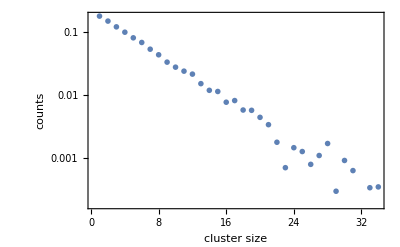

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
cp1000=ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]])},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8},{■, 8}, {○, 8}, {□, 8}}]
```

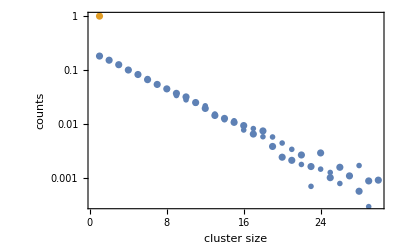

```mathematica
Show[pnew,cp1000]
```

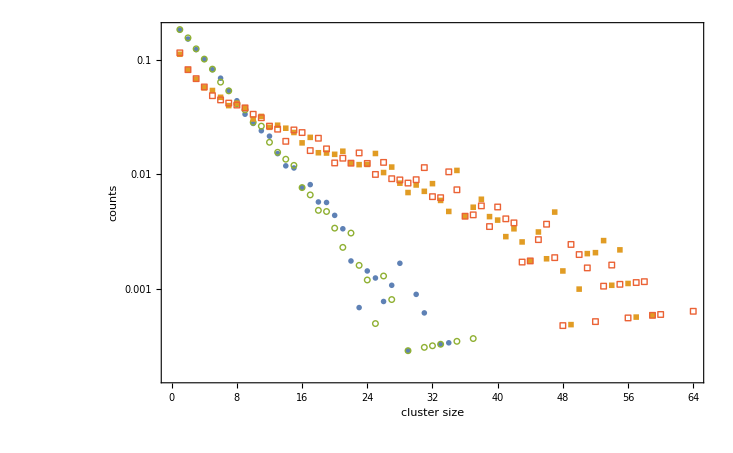

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
cp1000=ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[2]] hist[[2,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[1]]Mean[kmchist[[1]]])/nads[[1]],(size[[2]]Mean[kmchist[[2]]])/nads[[2]]},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8},{■, 8}, {○, 8}, {□, 8}}]
```

### nlat020T0600c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc\\nlat020T0600c0250"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc\nlat020T0600c0250

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
```

{{20,20},{100,100}}

{1001,101}

```mathematica
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[1,2;;;;2]]];
kmchist=data[[1,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[1,All,2]]],Variance[energy[[1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-1.27716,0.0450927}

Part::partd: Part specification kmcefiles⟦1,All,2⟧ is longer than depth of object.

{Mean[kmcefiles⟦1,All,2⟧],Variance[kmcefiles⟦1,All,2⟧]}

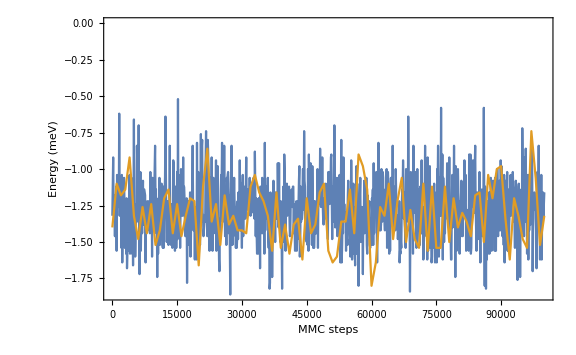

```mathematica
energyplot=ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

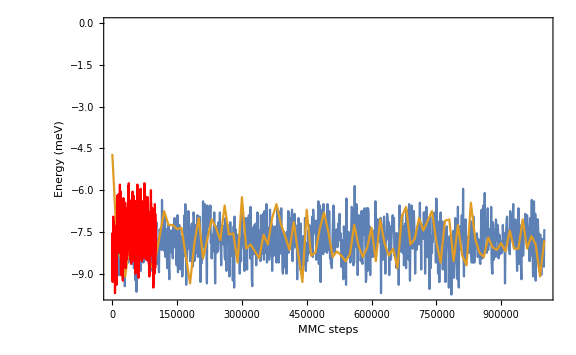

```mathematica
Show[energyplot,kmcenplot]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1, 1.5nlat[[1]]},{-1,nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[1]]},{-3,3nlat[[1]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

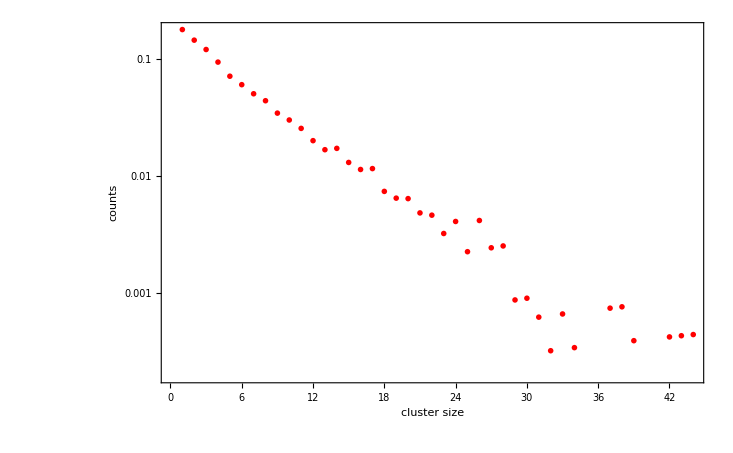

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
cp600=ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]])(*,(size[[1]]Mean[kmchist])/nads[[1]]*)},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8}, {○, 8}},PlotStyle->Red]
```

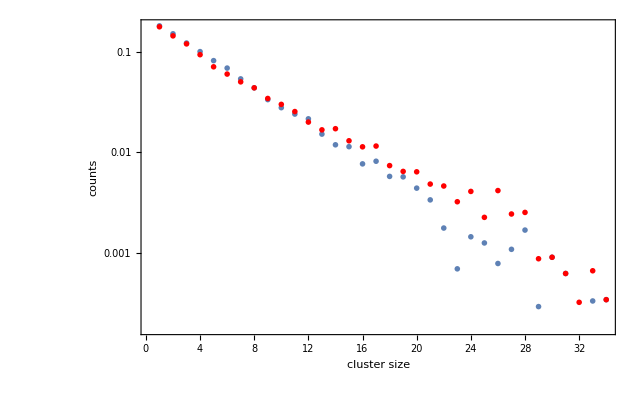

```mathematica
Show[cp1000,cp600]
```

## Compare MMC and KMC V0.1

### nlat020T1000c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en,mmc_melt.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

{{20,20,20},{100,100,100}}

{1001,101,101}

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[1,2;;;;2]]];
kmchist=data[[1,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[1,All,2]]],Variance[energy[[1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-5.42707,0.213671}

{-5.38195,0.222709}

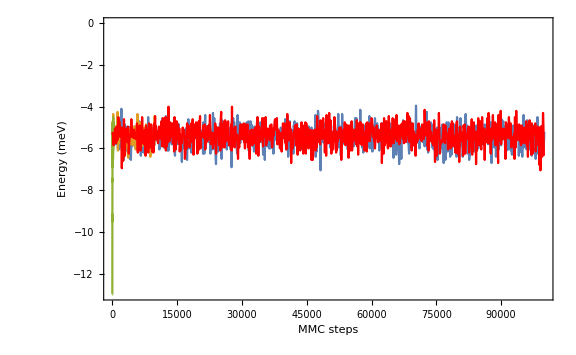

```mathematica
Show[ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large],kmcenplot]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1,1 1.5nlat[[1]]},{-1,1nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[1]]},{-3,3nlat[[1]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

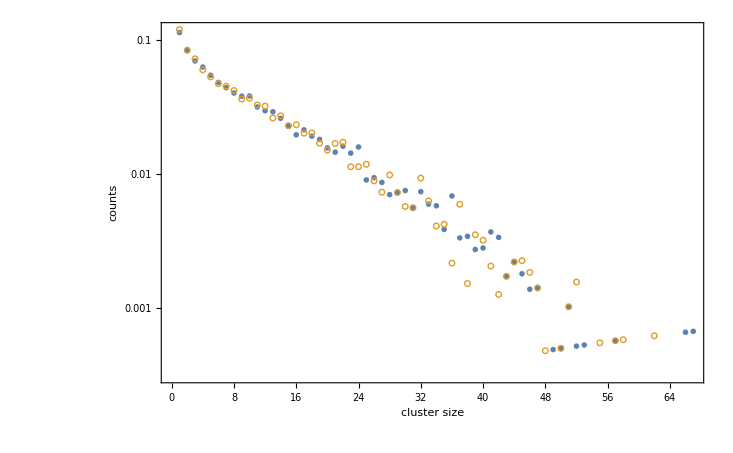

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[1]]Mean[kmchist])/nads[[1]]},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8}, {○, 8}}]
```

### nlat020T0600c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
```

{{20,20},{100,100}}

{1001,101}

```mathematica
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[1,2;;;;2]]];
kmchist=data[[1,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[1,All,2]]],Variance[energy[[1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-7.80659,0.454796}

{-7.58885,0.455564}

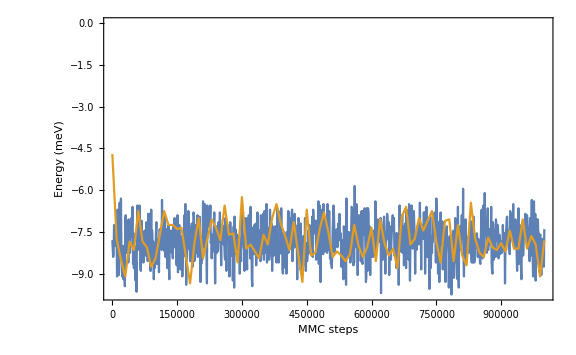

```mathematica
energyplot=ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

```mathematica
Show[energyplot,kmcenplot]
```

-Graphics-

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1, 1.5nlat[[1]]},{-1,nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[1]]},{-3,3nlat[[1]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

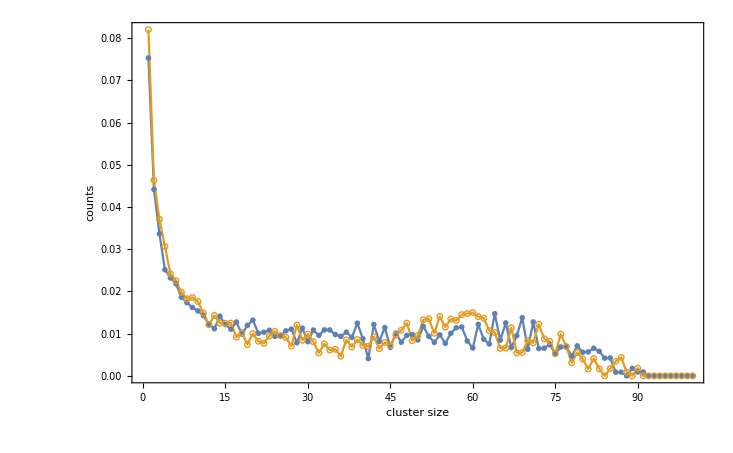

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
ListLinePlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[1]]Mean[kmchist])/nads[[1]]},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8}, {○, 8}}]
```